### [i,k] — Перемещения в направлении i, от нагрузки, равномерно распределённой в направлении k, по прямоугольной области(a на b) в виде скомпилированных функций

```mathematica
U[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

### [i,j,k] — Напряжения i,j от нагрузки равномерно распределённой в направлении k, по прямоугольной области (a на b) в виде скомпилированных функций

```mathematica
σ[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;
b=0.5;a=1; P0=-1;
bx=1;by=1;
```

## Графики

### Графики напряжений

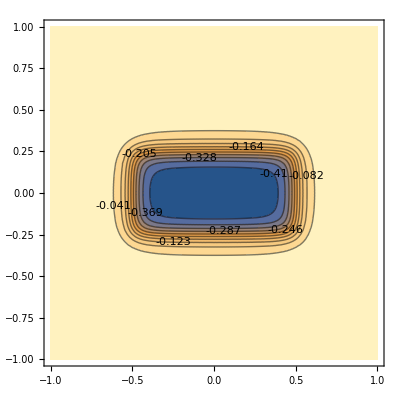

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

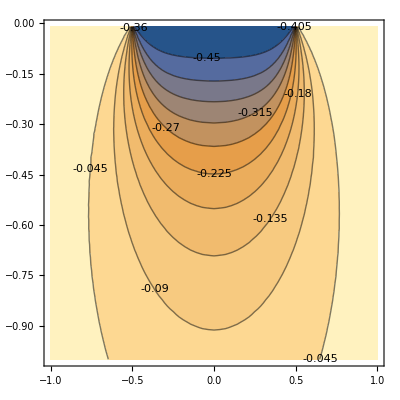

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

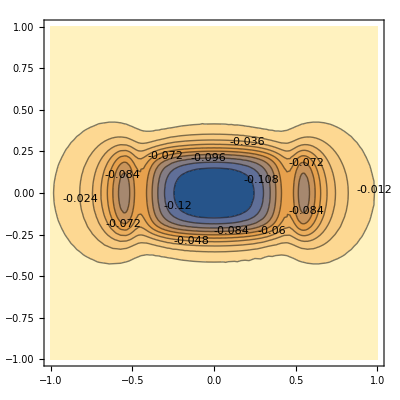

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

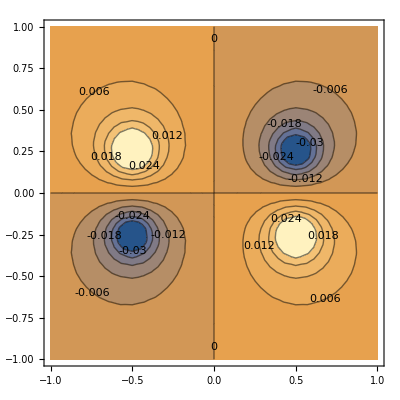

```mathematica
Print[ContourPlot[σ[1,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

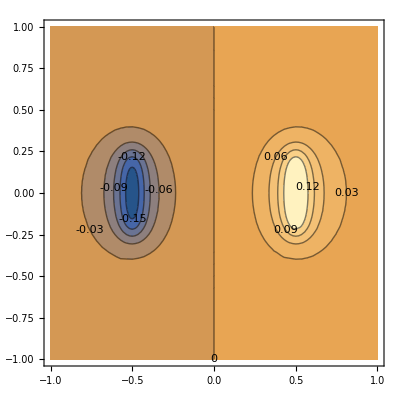

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

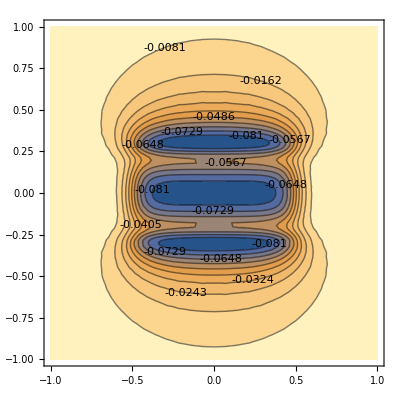

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

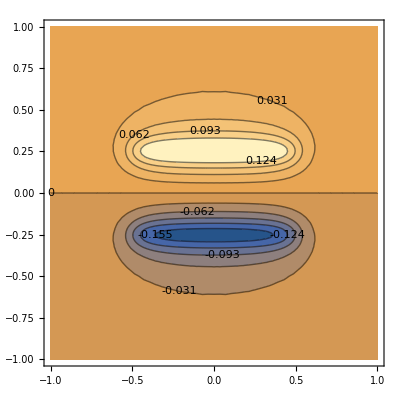

```mathematica
Print[ContourPlot[σ[2,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

### Графики перемещений

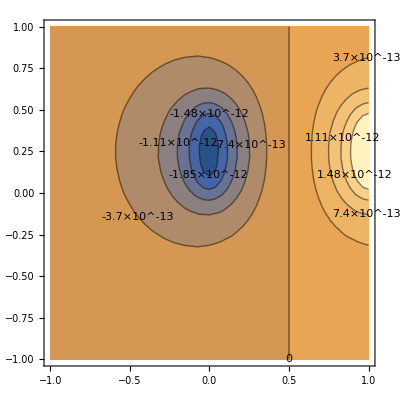

```mathematica
Print[ContourPlot[U[1,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

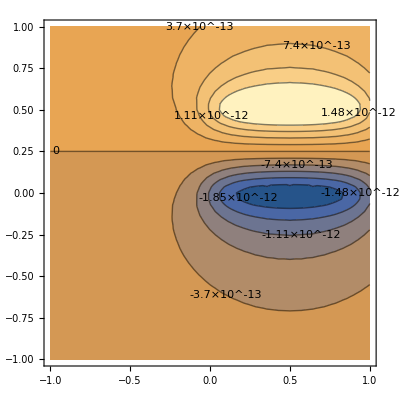

```mathematica
Print[ContourPlot[U[2,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

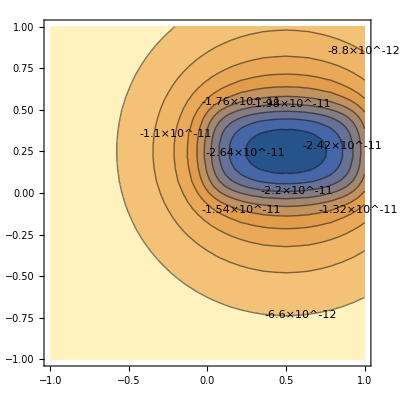

```mathematica
Print[ContourPlot[U[3,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```